```mathematica
nocc=1;
Table[
Table[
Table[
res[N[gfac/10]][nbas][omega]= ReadList["/home/grining/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[gfac]<>".out_FCCD"][[1]]
,{gfac, {10}}];
,{nbas, 4, 19}];
,{omega,1,20}];
```

ReadList::noopen: Cannot open /home/grining/drake-mpfun/python/results/nocc=1nbas=12omega=20gfac=10.out_FCCD.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

ReadList::noopen: Cannot open /home/grining/drake-mpfun/python/results/nocc=1nbas=13omega=20gfac=10.out_FCCD.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReadList::noopen: Cannot open /home/grining/drake-mpfun/python/results/nocc=1nbas=14omega=20gfac=10.out_FCCD.

General::stop: Further output of ReadList::noopen will be suppressed during this calculation.

```mathematica
fit= NonlinearModelFit[Table[{omega,res[1.0][8][omega]}, {omega, 5, 20}],a Exp[-b x]+c,{a,b,c},x]
```

FittedModel[1.306861344877776297098041329879959011958+0.1815422688792765345573474511849194320159 ⅇ^(-«79» x)]

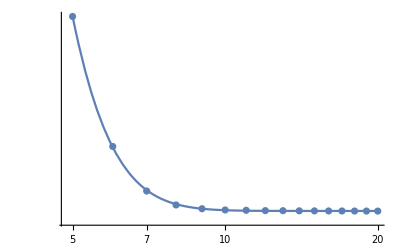

```mathematica
Show[
{
ListLogLogPlot[Table[{omega,res[1.0][7][omega]}, {omega,5, 20}], PlotRange->All],
LogLogPlot[fit[x],{x,5,20}, PlotRange->All]
}
]
```

```mathematica
fit= NonlinearModelFit[Table[{nbas,res[1.0][nbas][9]}, {nbas,4,18,2}],a Exp[-b x]+c,{a,b,c},x]
```

FittedModel[1.306860115575708351304655645799047912679+0.005667816566669267701040979125649524095607 ⅇ^(-«79» x)]

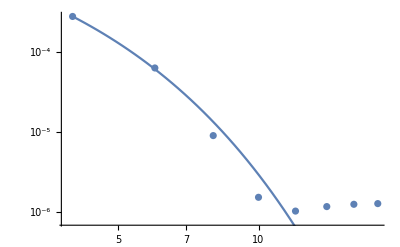

```mathematica
Show[
{
ListLogLogPlot[Table[{nbas,res[1.0][nbas][9]-fit[[1]][[2]][[3]][[2]]}, {nbas,4, 18, 2}], PlotRange->All],
LogLogPlot[fit[x]-fit[[1]][[2]][[3]][[2]],{x,4,18}]
}
]
```

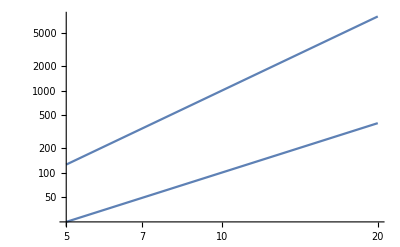

```mathematica
Show[
{
LogLogPlot[x^2, {x, 5, 20},PlotRange->All],
LogLogPlot[x^3, {x, 5, 20},PlotRange->All]
}
]
```